# Experiment 30a: Interaction of γ-rays with matter

## In-lab preliminary analysis

### 0.66 MeV Full Energy Peak

```mathematica
(* We import the Cs-137 spectrum. *)
```

```mathematica
<<CurveFit`
```

CurveFit for Mathematica v7.x thru v11.x, Version 1.96, 4/4/2018

Caltech Sophomore Physics Labs, Pasadena, CA

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/cesium137.tsv

File comment header:

Spectrum Name:
Description:
Student ID:
Detector Used:
Comments:
Acquisition Mode:	PHA
High Voltage:	920
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.15
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	729.15
Live Time Elapsed:	707.71
Start Time:	04/12/2018 14:05:16
Stop Time:	04/12/2018 14:17:25

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
(* We assign Posson uncertainties to the spectrum, taking the observed count for each bin as our maximum likelihood estimator of the expected count *)
```

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

```mathematica
(* We select the 0.66 MeV peak *)
```

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{439.57,475.48}

n= 36

2 points removed.

```mathematica
(* We now attempt a Gaussian+Linear fit of the 0.66 MeV peak *)
```

```mathematica
GaussianLFit[]
```

n = 38

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
-799.68 | d= 
-82.5839 |  | 
σ_c= 
1066.99 | σ_d= 
12.1342 |  | 
y_max= 
32884.3 | μ= 
457.964 | sigma= 
13.6919 | 
σ_y_max= 
1023.38 | σ_μ= 
0.114433 | σ_sigma= 
0.31642 | Std. deviation= 
205.981

Fit of (x,y±σ_y)

c= 
-854.639 | d= 
-81.196 |  | 
σ_c= 
692.739 | σ_d= 
7.92513 |  | 
y_max= 
32936.6 | μ= 
457.95 | sigma= 
13.7094 | 
σ_y_max= 
665.415 | σ_μ= 
0.0800416 | σ_sigma= 
0.215656 | χ^2/(n-5)= 
1.69725

Fit of (x±σ_x,y±σ_y)

Calculating sigm

c= 
-854.481 | d= 
-81.196 |  | 
σ_c= 
692.989 | σ_d= 
7.92824 |  | 
y_max= 
32936.4 | μ= 
457.95 | sigma= 
13.7094 | 
σ_y_max= 
665.693 | σ_μ= 
0.0799749 | σ_sigma= 
0.21572 | χ^2/(n-5)= 
1.69678

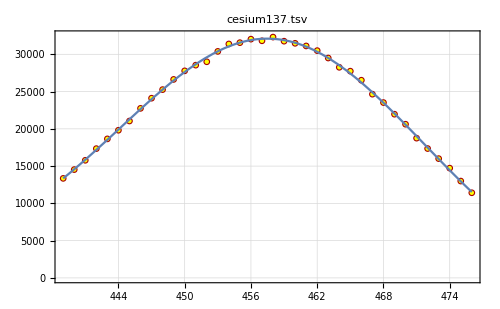
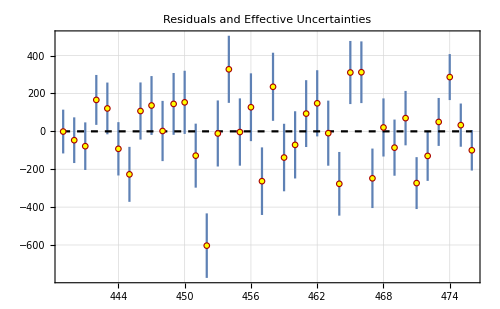
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
-854.481 | d= 
-81.196 |  | 
σ_c= 
692.989 | σ_d= 
7.92824 |  | 
y_max= 
32936.4 | μ= 
457.95 | sigma= 
13.7094 | 
σ_y_max= 
665.693 | σ_μ= 
0.0799749 | σ_sigma= 
0.21572 | χ^2/(n-5)= 
1.69678

```mathematica
LinearDifferencePlot[]
```

A reasonably good Gaussian+Linear fit is obtained ((χ̃)^2=1.69), indicating that the distribution limiting the energy resolution described by Poisson statistics approximates a Gaussian as described in the lab manual.

### Rate-related Gain Shift

```mathematica
(* We control for rate-related gain shift by observing the spectra for Cs-137 with the source near and far from the photomultiplier. First, we show the spectrum when the source is far from the photomultiplier. *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/cesium137.tsv

File comment header:

Spectrum Name:
Description:
Student ID:
Detector Used:
Comments:
Acquisition Mode:	PHA
High Voltage:	920
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.15
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	729.15
Live Time Elapsed:	707.71
Start Time:	04/12/2018 14:05:16
Stop Time:	04/12/2018 14:17:25

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

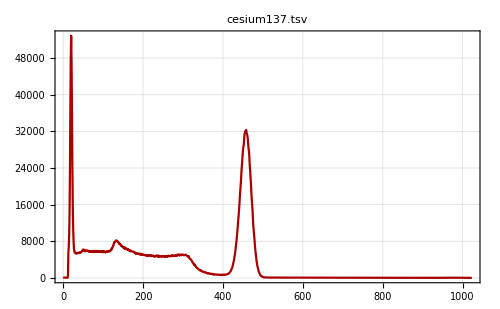

```mathematica
LinearDataPlot[]
```

```mathematica
(* We now show the spectrum when the source is near the photomultiplier. *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/betternear.tsv

File comment header:

Spectrum Name:
Description:
Student ID:
Detector Used:
Comments:
Acquisition Mode:	PHA
High Voltage:	840
Conversion Gain:	1024
Course Gain:	16
Fine Gain:	1.15
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	786.18
Live Time Elapsed:	779.87
Start Time:	04/12/2018 13:22:54
Stop Time:	04/12/2018 13:36:01

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

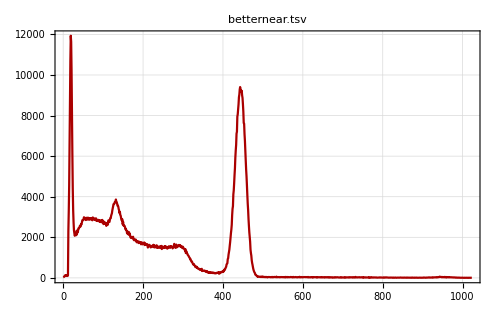

```mathematica
LinearDataPlot[]
```

```mathematica
(* We obtain the position of the 0.66 MeV peak as before by fitting the 0.66 MeV peak against a Gaussian+Linear and fiding the μ. *)
```

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{423.38,466.36}

n= 43

21 points removed.

```mathematica
GaussianLFit[]
```

n = 43

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
311.766 | d= 
-22.2878 |  | 
σ_c= 
206.891 | σ_d= 
3.09053 |  | 
y_max= 
9021.57 | μ= 
444.682 | sigma= 
13.0977 | 
σ_y_max= 
211.677 | σ_μ= 
0.115593 | σ_sigma= 
0.268319 | Std. deviation= 
87.2277

Fit of (x,y±σ_y)

c= 
297.561 | d= 
-22.0465 |  | 
σ_c= 
159.15 | σ_d= 
2.39169 |  | 
y_max= 
9033.77 | μ= 
444.674 | sigma= 
13.1145 | 
σ_y_max= 
163.931 | σ_μ= 
0.0999738 | σ_sigma= 
0.211216 | χ^2/(n-5)= 
1.13694

Fit of (x±σ_x,y±σ_y)

c= 
297.559 | d= 
-22.0464 |  | 
σ_c= 
159.204 | σ_d= 
2.39246 |  | 
y_max= 
9033.77 | μ= 
444.674 | sigma= 
13.1145 | 
σ_y_max= 
163.995 | σ_μ= 
0.0999985 | σ_sigma= 
0.211323 | χ^2/(n-5)= 
1.1366

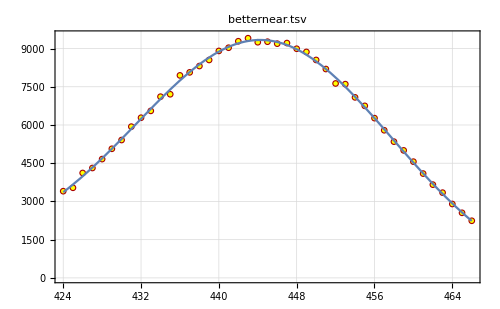
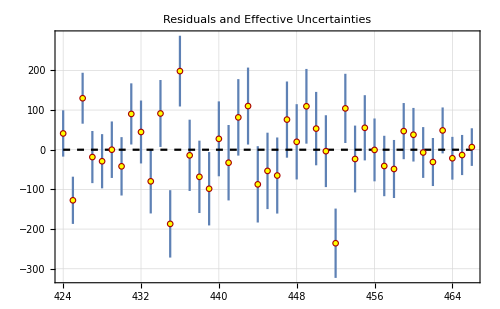
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
297.559 | d= 
-22.0464 |  | 
σ_c= 
159.204 | σ_d= 
2.39246 |  | 
y_max= 
9033.77 | μ= 
444.674 | sigma= 
13.1145 | 
σ_y_max= 
163.995 | σ_μ= 
0.0999985 | σ_sigma= 
0.211323 | χ^2/(n-5)= 
1.1366

```mathematica
LinearDifferencePlot[]
```

We observe a shift in the position of the peak of about 13 channels, or less than 3%. We therefore have significant rate-related gain shift in our spectra and may have to carry out the experiment again while controlling for rate at the detector. We may also have to account for the systematic error introduced by the shift (and the drift described in the next section) in the data analysis.

### Long-term stability of gain

We similarly verify the long-term stability of the system’s gain by comparing Co-60 spectra taken at an interval of each other and observing any drift in the position of the peaks. We accurately find the positions of the peaks using the same procedure as above (fit Gaussian+Linear to full-energy a full energy peak, and the mean μ will give a maximum likelihood estimator of the position of the peak).

```mathematica
(* We find the position of one of the Co-60 peaks for the first spectrum. *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/cobalt60.tsv

File comment header:

Spectrum Name:
Description:
Student ID:
Detector Used:
Comments:
Acquisition Mode:	PHA
High Voltage:	920
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.15
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	1393.61
Live Time Elapsed:	1330.01
Start Time:	04/12/2018 13:41:10
Stop Time:	04/12/2018 14:04:23

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{772.54,820.82}

n= 48

8 points removed.

```mathematica
GaussianLFit[]
```

n = 48

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
1573.11 | d= 
-26.0931 |  | 
σ_c= 
732.922 | σ_d= 
7.00643 |  | 
y_max= 
17430.9 | μ= 
797.48 | sigma= 
18.1245 | 
σ_y_max= 
805.072 | σ_μ= 
0.207815 | σ_sigma= 
0.451069 | Std. deviation= 
145.581

Fit of (x,y±σ_y)

c= 
1406.07 | d= 
-27.4488 |  | 
σ_c= 
583.721 | σ_d= 
5.38511 |  | 
y_max= 
17591. | μ= 
797.52 | sigma= 
18.2437 | 
σ_y_max= 
624.201 | σ_μ= 
0.166641 | σ_sigma= 
0.384861 | χ^2/(n-5)= 
1.49816

Fit of (x±σ_x,y±σ_y)

c= 
1406.1 | d= 
-27.4483 |  | 
σ_c= 
583.759 | σ_d= 
5.38559 |  | 
y_max= 
17591. | μ= 
797.52 | sigma= 
18.2437 | 
σ_y_max= 
624.25 | σ_μ= 
0.166652 | σ_sigma= 
0.384855 | χ^2/(n-5)= 
1.49795

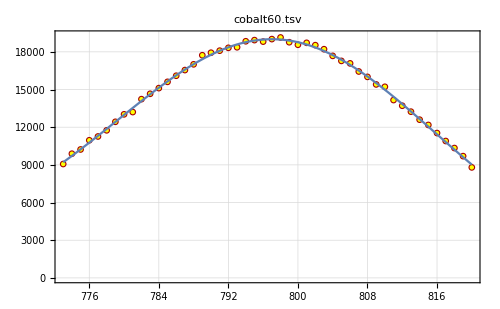
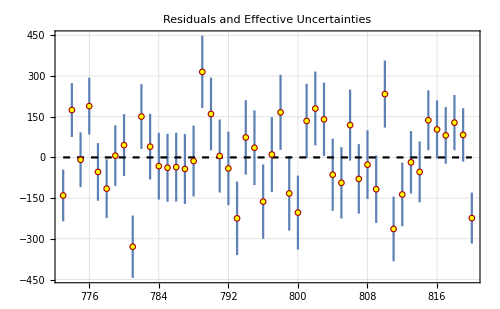
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
1406.1 | d= 
-27.4483 |  | 
σ_c= 
583.759 | σ_d= 
5.38559 |  | 
y_max= 
17591. | μ= 
797.52 | sigma= 
18.2437 | 
σ_y_max= 
624.25 | σ_μ= 
0.166652 | σ_sigma= 
0.384855 | χ^2/(n-5)= 
1.49795

```mathematica
LinearDifferencePlot[]
```

```mathematica
(* We now do the same for the second Co-60 spectrum. *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/co60second.tsv

File comment header:

Spectrum Name:
Description:
Student ID:
Detector Used:
Comments:
Acquisition Mode:	PHA
High Voltage:	920
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.15
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	759.3
Live Time Elapsed:	754.16
Start Time:	04/12/2018 14:49:39
Stop Time:	04/12/2018 15:02:18

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{762.2,821.2}

n= 59

965 points removed.

```mathematica
GaussianLFit[]
```

n = 59

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
123.199 | d= 
-1.90007 |  | 
σ_c= 
73.9997 | σ_d= 
0.884357 |  | 
y_max= 
1367.89 | μ= 
793.752 | sigma= 
18.2228 | 
σ_y_max= 
83.01 | σ_μ= 
0.399633 | σ_sigma= 
0.76857 | Std. deviation= 
34.6833

Fit of (x,y±σ_y)

c= 
107.421 | d= 
-2.04655 |  | 
σ_c= 
62.527 | σ_d= 
0.721405 |  | 
y_max= 
1381.51 | μ= 
793.809 | sigma= 
18.383 | 
σ_y_max= 
67.5309 | σ_μ= 
0.318476 | σ_sigma= 
0.800958 | χ^2/(n-5)= 
1.10925

Fit of (x±σ_x,y±σ_y)

c= 
107.41 | d= 
-2.04662 |  | 
σ_c= 
62.5355 | σ_d= 
0.721534 |  | 
y_max= 
1381.52 | μ= 
793.809 | sigma= 
18.3831 | 
σ_y_max= 
67.5434 | σ_μ= 
0.318507 | σ_sigma= 
0.801073 | χ^2/(n-5)= 
1.10908

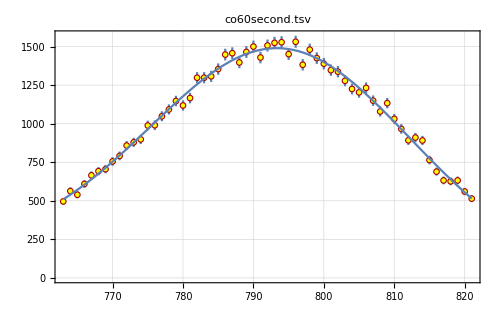
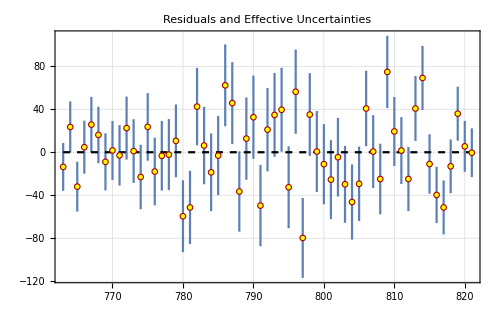
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
107.41 | d= 
-2.04662 |  | 
σ_c= 
62.5355 | σ_d= 
0.721534 |  | 
y_max= 
1381.52 | μ= 
793.809 | sigma= 
18.3831 | 
σ_y_max= 
67.5434 | σ_μ= 
0.318507 | σ_sigma= 
0.801073 | χ^2/(n-5)= 
1.10908

```mathematica
LinearDifferencePlot[]
```

We observe a shift in the peak position of about 4 channels or 0.5%, such that small but observable drift occurs. The response of the system is relatively stable with respect to time, but we will have to consider in what way the observed drift affects our estimate for the uncertainties in our peak positions (for instance, what type of error this contributes to).

### Background spectrum

A spectrum of the background noise is taken over several minutes, to be used as a baseline.

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/background.tsv

File comment header:

Spectrum Name:
Description:
Student ID:
Detector Used:
Comments:
Acquisition Mode:	PHA
High Voltage:	920
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.15
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	258.63
Live Time Elapsed:	257.8
Start Time:	04/12/2018 15:39:34
Stop Time:	04/12/2018 15:43:52

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

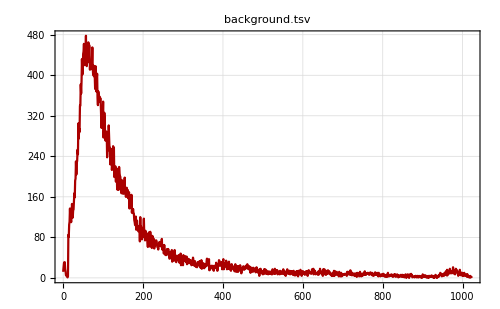

```mathematica
LinearDataPlot[]
```

We observe that the count is small enough that the background will not contribute to observable features of the spectra.

By a rough calibration using the peaks above, we observed a peak with increased counts at ~0.1 MeV. This may correspond to the NaI K-edge as described in the photoelectric absorption section of the lab manual.

## Data Analysis

```mathematica
(* We consider a small, flat portion of the C-137 spectrum and fit to a constant to observe the channel-to-channel scatter. *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/cesium137.tsv

File comment header:

Spectrum Name:
Description:
Student ID:
Detector Used:
Comments:
Acquisition Mode:	PHA
High Voltage:	920
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.15
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	729.15
Live Time Elapsed:	707.71
Start Time:	04/12/2018 14:05:16
Stop Time:	04/12/2018 14:17:25

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{532.,599.4}

n= 68

956 points removed.

```mathematica
ConstantFit[]
```

n = 68

y(x) = a

Fit of (x,y)  (unweighted)

a= 
60.9706 | 
σ_a= 
0.978695 | Std. deviation= 
8.07053

Fit of (x,y±σ_y)

a= 
59.9112 | 
σ_a= 
0.938641 | χ^2/(n-1)= 
1.07515

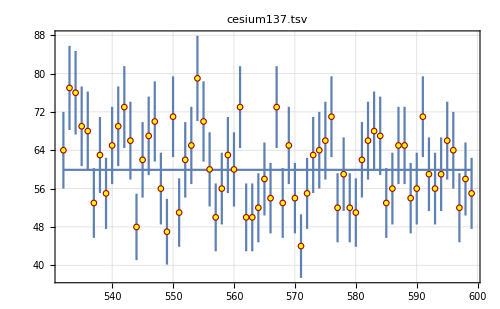
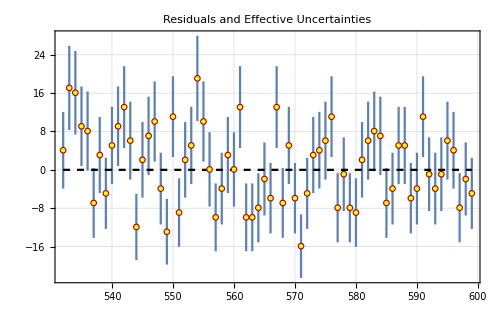
-Graphics-
-Graphics-
y(x) = a
a= 
59.9112 | 
σ_a= 
0.938641 | χ^2/(n-1)= 
1.07515

```mathematica
LinearDifferencePlot[]
```

As expected, the linear background very closely fits a constant, with a reduced (χ̃)^2very close to 1. The residual plot also allows us to observe that the channel-to-channel scatter should not be significant over high-count features and will not pose an issue when interpreting the spectra of short half-life isotopes, despite being significant with respect to the background count (we will observe a noise feature due to the K-edge of NaI for longer half-life isotopes such as Na-22).

### Cs-137 spectrum

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/cesium137.tsv

File comment header:

Spectrum Name:
Description:
Student ID:
Detector Used:
Comments:
Acquisition Mode:	PHA
High Voltage:	920
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.15
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	729.15
Live Time Elapsed:	707.71
Start Time:	04/12/2018 14:05:16
Stop Time:	04/12/2018 14:17:25

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
LinearDataPlot[]
```

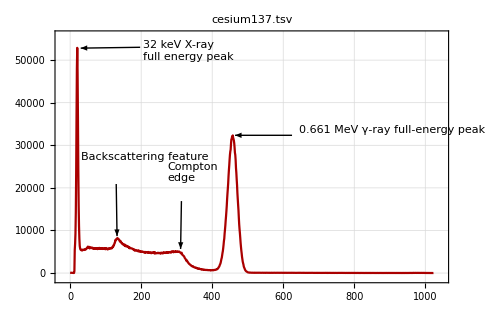

### Na-22 spectrum

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/na22.tsv

File comment header:

Spectrum Name:
Description:
Student ID:
Detector Used:
Comments:
Acquisition Mode:	PHA
High Voltage:	920
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.15
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	650.45
Live Time Elapsed:	648.97
Start Time:	04/12/2018 14:36:48
Stop Time:	04/12/2018 14:47:47

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
LinearDataPlot[]
```

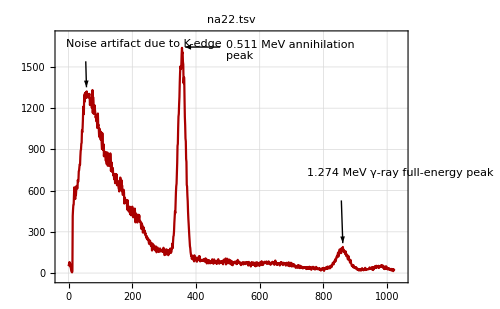

### Co-60 spectrum

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/cobalt60.tsv

File comment header:

Spectrum Name:
Description:
Student ID:
Detector Used:
Comments:
Acquisition Mode:	PHA
High Voltage:	920
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.15
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	1393.61
Live Time Elapsed:	1330.01
Start Time:	04/12/2018 13:41:10
Stop Time:	04/12/2018 14:04:23

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
LinearDataPlot[]
```

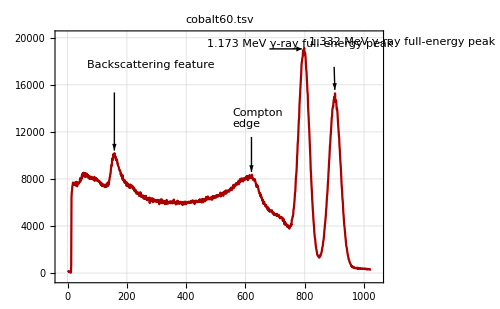

### Co-57 spectrum

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/co57.tsv

File comment header:

Spectrum Name:
Description:
Student ID:
Detector Used:
Comments:
Acquisition Mode:	PHA
High Voltage:	920
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.15
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	2138.93
Live Time Elapsed:	2135.44
Start Time:	04/12/2018 15:03:19
Stop Time:	04/12/2018 15:38:57

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

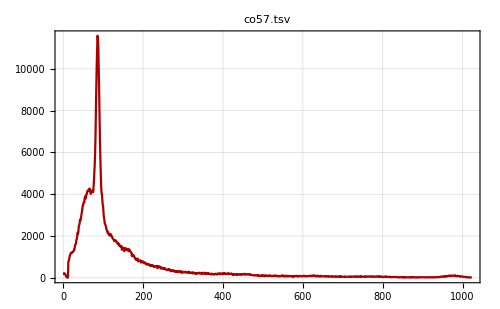

```mathematica
LinearDataPlot[]
```

```mathematica
(* We select the leftmost section of the spectrum to better discern any interesting features. *)
```

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{-21.3125,200.}

n= 201

823 points removed.

```mathematica
LinearDataPlot[]
```

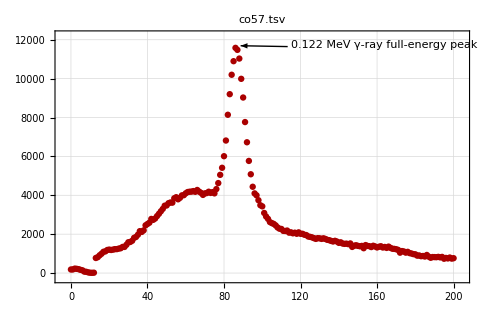

The 0.136 γ-ray full energy peak has a low count (as expected) and cannot be clearly discerned, and therefore will be left out of the calibration set. The 0.0144 MeV γ-ray full energy peak is too close to the LLD to be reliably discerned, and will also be left out of the calibration set.

### Ba-133 spectrum

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/barium133.tsv

File comment header:

Spectrum Name:
Description:
Student ID:
Detector Used:
Comments:
Acquisition Mode:	PHA
High Voltage:	920
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.15
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	1004.14
Live Time Elapsed:	837.5
Start Time:	04/12/2018 14:18:22
Stop Time:	04/12/2018 14:35:06

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

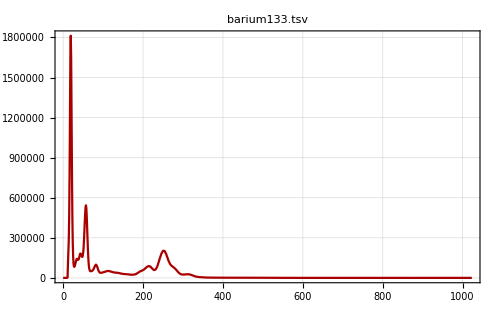

```mathematica
LinearDataPlot[]
```

```mathematica
(* We again select the leftmost section of the spectrum to better discern any interesting features. *)
```

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{-21.3125,451.6}

n= 452

572 points removed.

```mathematica
LinearDataPlot[]
```

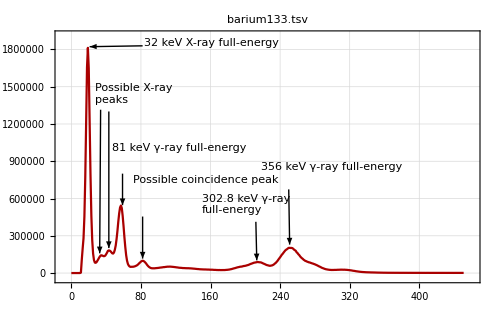

Other features we would expect to see from the decay cycle of Ba-133 are not clearly discernible and therefore not labelled inMinimizing Chi^2 the above figure. We only consider the full-energy peaks for the calibration set, because those are reliably located on the spectrum above. We may have to exclude the 302.8 keV peak if we find that it is too close to the larger 356 keV peak and that they have superposed significantly near the 302.8 keV peak, skewing the Gaussian+Linear fit.

## Constructing calibration dataset

```mathematica
(* Define loop to prompt for selection of peak from data in file, then returns fit and prompt for appending {energy, mean, sigmean} to calibration dataset calData *)

SetDirectory[NotebookDirectory[]];
fileList={"na22.tsv","barium133.tsv","cesium137.tsv","co57.tsv","cobalt60.tsv"};
calData={{"Energy (MeV)","mean","sigmean"}};
ClearAll[energy]

For[
i=1,
i≤Length[fileList],
(
Block[
{Print},
LoadFile[fileList[[i]], SkipLines->{"Data:","Counts"}];
MakePoisson[Xerrors -> True];
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
];
GaussianLFit[];
DialogInput[
Grid[
{
{"Energy (MeV):",InputField[Dynamic[energy],Number]},
{
CancelButton[DialogReturn[]],
DefaultButton[DialogReturn[(AppendTo[calData,{energy,mean,sigmean}];)]],
Button["Next",DialogReturn[(AppendTo[calData,{energy,mean,sigmean}];i++;)]]
}
},
Spacings->{1,Automatic},Alignment->Left]
];
)
]

calData=Table[If[calData[[i]][[1]]==0,Null,calData[[i]]],{i,Length[calData]}]/.Null->Sequence[];
```

n = 66

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

Calculating sigc

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0,0,0.18672,0} from the point {857.159,-28.7019,3.91548×10^8,-0.264642}.

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {8.59878,0,0,0} from the point {859.878,143.393,18.672,-0.16352}.

c= 
23.1441 | d= 
-0.16352 |  | 
σ_c= 
√(0.0527148+1/4 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 (78.7051-CurveFit`Private`e1) CurveFit`Private`e3))/(CurveFit`Private`e3)]^2) | σ_d= 
0.163008 |  | 
y_max= 
143.393 | μ= 
859.878 | sigma= 
18.672 | 
σ_y_max= 
17.4716 | σ_μ= 
0.849297 | σ_sigma= 
2.06714 | Std. deviation= 
9.99555

Fit of (x,y±σ_y)

c= 
21.3237 | d= 
-0.224641 |  | 
σ_c= 
12.3314 | σ_d= 
0.147204 |  | 
y_max= 
143.996 | μ= 
860.215 | sigma= 
18.8567 | 
σ_y_max= 
15.8205 | σ_μ= 
0.872824 | σ_sigma= 
2.00937 | χ^2/(n-5)= 
0.801373

Fit of (x±σ_x,y±σ_y)

c= 
21.3223 | d= 
-0.224648 |  | 
σ_c= 
12.3324 | σ_d= 
0.147203 |  | 
y_max= 
143.998 | μ= 
860.215 | sigma= 
18.8568 | 
σ_y_max= 
15.8242 | σ_μ= 
0.872803 | σ_sigma= 
2.00974 | χ^2/(n-5)= 
0.801284

n = 87

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
26.2556 | d= 
-0.0259917 |  | 
σ_c= 
4.23377 | σ_d= 
0.0617845 |  | 
y_max= 
140.754 | μ= 
859.281 | sigma= 
18.2486 | 
σ_y_max= 
4.30804 | σ_μ= 
0.46755 | σ_sigma= 
0.763193 | Std. deviation= 
9.08775

Fit of (x,y±σ_y)

c= 
26.6742 | d= 
-0.0188029 |  | 
σ_c= 
3.31715 | σ_d= 
0.0476377 |  | 
y_max= 
139.888 | μ= 
859.21 | sigma= 
18.048 | 
σ_y_max= 
3.54611 | σ_μ= 
0.480489 | σ_sigma= 
0.709563 | χ^2/(n-5)= 
0.784839

Fit of (x±σ_x,y±σ_y)

c= 
26.6736 | d= 
-0.0188026 |  | 
σ_c= 
3.31742 | σ_d= 
0.047641 |  | 
y_max= 
139.889 | μ= 
859.21 | sigma= 
18.0481 | 
σ_y_max= 
3.54638 | σ_μ= 
0.480527 | σ_sigma= 
0.709645 | χ^2/(n-5)= 
0.784743

n = 7

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

Calculating sigm

Calculating sigd

c= 
179167. | d= 
-15826.2 |  | 
σ_c= 
44455.3 | σ_d= 
3314.35 |  | 
y_max= 
361930. | μ= 
57.3355 | sigma= 
2.95539 | 
σ_y_max= 
70914.2 | σ_μ= 
0.105799 | σ_sigma= 
0.326736 | Std. deviation= 
1588.03

Fit of (x,y±σ_y)

c= 
172157. | d= 
-15401.5 |  | 
σ_c= 
21705.1 | σ_d= 
1624.83 |  | 
y_max= 
369364. | μ= 
57.3238 | sigma= 
2.98848 | 
σ_y_max= 
24691.6 | σ_μ= 
0.0509942 | σ_sigma= 
0.117952 | χ^2/(n-5)= 
4.86701

Fit of (x±σ_x,y±σ_y)

c= 
172214. | d= 
-15405. |  | 
σ_c= 
21716. | σ_d= 
1625.1 |  | 
y_max= 
369307. | μ= 
57.3239 | sigma= 
2.98819 | 
σ_y_max= 
24708.3 | σ_μ= 
0.0510011 | σ_sigma= 
0.118052 | χ^2/(n-5)= 
4.85968

n = 42

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
210.931 | d= 
-72.7349 |  | 
σ_c= 
595.566 | σ_d= 
8.31069 |  | 
y_max= 
31904.2 | μ= 
457.881 | sigma= 
13.4029 | 
σ_y_max= 
597.599 | σ_μ= 
0.0866796 | σ_sigma= 
0.211616 | Std. deviation= 
205.711

Fit of (x,y±σ_y)

c= 
439.913 | d= 
-69.3564 |  | 
σ_c= 
364.539 | σ_d= 
4.94736 |  | 
y_max= 
31691. | μ= 
457.844 | sigma= 
13.3246 | 
σ_y_max= 
353.515 | σ_μ= 
0.0579258 | σ_sigma= 
0.134947 | χ^2/(n-5)= 
1.89462

Fit of (x±σ_x,y±σ_y)

c= 
439.53 | d= 
-69.3605 |  | 
σ_c= 
365.073 | σ_d= 
4.94933 |  | 
y_max= 
31691.3 | μ= 
457.844 | sigma= 
13.3247 | 
σ_y_max= 
353.573 | σ_μ= 
0.0579427 | σ_sigma= 
0.134994 | χ^2/(n-5)= 
1.89379

n = 32

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
-2698.61 | d= 
-116.408 |  | 
σ_c= 
2923.15 | σ_d= 
33.4252 |  | 
y_max= 
34752. | μ= 
458.21 | sigma= 
14.139 | 
σ_y_max= 
2894.17 | σ_μ= 
0.25781 | σ_sigma= 
0.737474 | Std. deviation= 
213.066

Fit of (x,y±σ_y)

c= 
-2713.12 | d= 
-116.103 |  | 
σ_c= 
1960.78 | σ_d= 
22.8468 |  | 
y_max= 
34764.4 | μ= 
458.208 | sigma= 
14.1437 | 
σ_y_max= 
1935.42 | σ_μ= 
0.135372 | σ_sigma= 
0.505405 | χ^2/(n-5)= 
1.67788

Fit of (x±σ_x,y±σ_y)

c= 
-2713.1 | d= 
-116.103 |  | 
σ_c= 
1961.31 | σ_d= 
22.8533 |  | 
y_max= 
34764.4 | μ= 
458.208 | sigma= 
14.1437 | 
σ_y_max= 
1935.96 | σ_μ= 
0.135396 | σ_sigma= 
0.505531 | χ^2/(n-5)= 
1.67761

n = 14

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
3812.15 | d= 
-4.01484 |  | 
σ_c= 
389.503 | σ_d= 
24.7696 |  | 
y_max= 
7724.16 | μ= 
86.4308 | sigma= 
3.99369 | 
σ_y_max= 
420.928 | σ_μ= 
0.0949224 | σ_sigma= 
0.182978 | Std. deviation= 
96.2006

Fit of (x,y±σ_y)

c= 
3725.06 | d= 
2.65876 |  | 
σ_c= 
366.998 | σ_d= 
26.3922 |  | 
y_max= 
7805.96 | μ= 
86.4052 | sigma= 
4.02823 | 
σ_y_max= 
400.45 | σ_μ= 
0.0924462 | σ_sigma= 
0.173431 | χ^2/(n-5)= 
0.971488

Fit of (x±σ_x,y±σ_y)

c= 
3725.29 | d= 
2.64232 |  | 
σ_c= 
367.209 | σ_d= 
26.4001 |  | 
y_max= 
7805.74 | μ= 
86.4053 | sigma= 
4.02813 | 
σ_y_max= 
400.566 | σ_μ= 
0.0924888 | σ_sigma= 
0.173479 | χ^2/(n-5)= 
0.970584

n = 53

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
1424.63 | d= 
-27.357 |  | 
σ_c= 
472.606 | σ_d= 
4.59517 |  | 
y_max= 
17576.3 | μ= 
797.514 | sigma= 
18.2235 | 
σ_y_max= 
488.472 | σ_μ= 
0.150419 | σ_sigma= 
0.381202 | Std. deviation= 
139.444

Fit of (x,y±σ_y)

c= 
1364.38 | d= 
-28.0836 |  | 
σ_c= 
366.595 | σ_d= 
3.45276 |  | 
y_max= 
17632.1 | μ= 
797.539 | sigma= 
18.269 | 
σ_y_max= 
371.377 | σ_μ= 
0.120937 | σ_sigma= 
0.312366 | χ^2/(n-5)= 
1.39289

Fit of (x±σ_x,y±σ_y)

c= 
1364.38 | d= 
-28.0833 |  | 
σ_c= 
366.631 | σ_d= 
3.45316 |  | 
y_max= 
17632.1 | μ= 
797.539 | sigma= 
18.269 | 
σ_y_max= 
371.418 | σ_μ= 
0.121034 | σ_sigma= 
0.312389 | χ^2/(n-5)= 
1.39269

n = 43

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
1894.74 | d= 
-14.3304 |  | 
σ_c= 
1033.31 | σ_d= 
9.0577 |  | 
y_max= 
17122.6 | μ= 
797.187 | sigma= 
17.8955 | 
σ_y_max= 
1205.54 | σ_μ= 
0.246095 | σ_sigma= 
0.836911 | Std. deviation= 
137.803

Fit of (x,y±σ_y)

c= 
1982.28 | d= 
-13.8131 |  | 
σ_c= 
872.118 | σ_d= 
7.63327 |  | 
y_max= 
17036.3 | μ= 
797.172 | sigma= 
17.8324 | 
σ_y_max= 
989.813 | σ_μ= 
0.217203 | σ_sigma= 
0.704616 | χ^2/(n-5)= 
1.18389

Fit of (x±σ_x,y±σ_y)

c= 
1982.24 | d= 
-13.8132 |  | 
σ_c= 
872.178 | σ_d= 
7.63381 |  | 
y_max= 
17036.4 | μ= 
797.172 | sigma= 
17.8324 | 
σ_y_max= 
989.899 | σ_μ= 
0.217217 | σ_sigma= 
0.704669 | χ^2/(n-5)= 
1.18379

n = 37

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
1824.24 | d= 
-14.1439 |  | 
σ_c= 
2024.17 | σ_d= 
16.6076 |  | 
y_max= 
17193.4 | μ= 
797.183 | sigma= 
17.9343 | 
σ_y_max= 
2818.95 | σ_μ= 
0.411938 | σ_sigma= 
1.75313 | Std. deviation= 
149.19

Fit of (x,y±σ_y)

c= 
2185.19 | d= 
-12.6437 |  | 
σ_c= 
1614.92 | σ_d= 
13.3505 |  | 
y_max= 
16837.2 | μ= 
797.143 | sigma= 
17.6929 | 
σ_y_max= 
2100.38 | σ_μ= 
0.331637 | σ_sigma= 
1.34967 | χ^2/(n-5)= 
1.37882

Fit of (x±σ_x,y±σ_y)

c= 
2184.94 | d= 
-12.6439 |  | 
σ_c= 
1615.05 | σ_d= 
13.3514 |  | 
y_max= 
16837.4 | μ= 
797.143 | sigma= 
17.6931 | 
σ_y_max= 
2100.62 | σ_μ= 
0.33166 | σ_sigma= 
1.3498 | χ^2/(n-5)= 
1.37871

n = 40

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
1855.43 | d= 
-13.5939 |  | 
σ_c= 
1432.51 | σ_d= 
11.9258 |  | 
y_max= 
17162.2 | μ= 
797.169 | sigma= 
17.9185 | 
σ_y_max= 
1789.88 | σ_μ= 
0.315377 | σ_sigma= 
0.97472 | Std. deviation= 
143.31

Fit of (x,y±σ_y)

c= 
2072.01 | d= 
-12.275 |  | 
σ_c= 
1175.44 | σ_d= 
9.72436 |  | 
y_max= 
16948.9 | μ= 
797.133 | sigma= 
17.7696 | 
σ_y_max= 
1407.91 | σ_μ= 
0.262999 | σ_sigma= 
0.855392 | χ^2/(n-5)= 
1.27613

Fit of (x±σ_x,y±σ_y)

c= 
2071.88 | d= 
-12.2754 |  | 
σ_c= 
1175.53 | σ_d= 
9.72507 |  | 
y_max= 
16949. | μ= 
797.133 | sigma= 
17.7697 | 
σ_y_max= 
1408.04 | σ_μ= 
0.263016 | σ_sigma= 
0.855473 | χ^2/(n-5)= 
1.27603

n = 40

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
1855.43 | d= 
-13.5939 |  | 
σ_c= 
1432.51 | σ_d= 
11.9258 |  | 
y_max= 
17162.2 | μ= 
797.169 | sigma= 
17.9185 | 
σ_y_max= 
1789.88 | σ_μ= 
0.315377 | σ_sigma= 
0.97472 | Std. deviation= 
143.31

Fit of (x,y±σ_y)

c= 
2072.01 | d= 
-12.275 |  | 
σ_c= 
1175.44 | σ_d= 
9.72436 |  | 
y_max= 
16948.9 | μ= 
797.133 | sigma= 
17.7696 | 
σ_y_max= 
1407.91 | σ_μ= 
0.262999 | σ_sigma= 
0.855392 | χ^2/(n-5)= 
1.27613

Fit of (x±σ_x,y±σ_y)

c= 
2071.88 | d= 
-12.2754 |  | 
σ_c= 
1175.53 | σ_d= 
9.72507 |  | 
y_max= 
16949. | μ= 
797.133 | sigma= 
17.7697 | 
σ_y_max= 
1408.04 | σ_μ= 
0.263016 | σ_sigma= 
0.855473 | χ^2/(n-5)= 
1.27603

n = 55

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
-243.436 | d= 
-0.239626 |  | 
σ_c= 
684.626 | σ_d= 
7.16951 |  | 
y_max= 
15146. | μ= 
901.211 | sigma= 
20.2037 | 
σ_y_max= 
678.048 | σ_μ= 
0.281953 | σ_sigma= 
0.606352 | Std. deviation= 
127.035

Fit of (x,y±σ_y)

Calculating sigm

c= 
-318.27 | d= 
0.858466 |  | 
σ_c= 
516.26 | σ_d= 
6.28205 |  | 
y_max= 
15218.4 | μ= 
901.167 | sigma= 
20.266 | 
σ_y_max= 
510.68 | σ_μ= 
0.236115 | σ_sigma= 
0.461859 | χ^2/(n-5)= 
1.32956

Fit of (x±σ_x,y±σ_y)

c= 
-318.246 | d= 
0.858739 |  | 
σ_c= 
516.325 | σ_d= 
6.28192 |  | 
y_max= 
15218.4 | μ= 
901.167 | sigma= 
20.2659 | 
σ_y_max= 
510.748 | σ_μ= 
0.236158 | σ_sigma= 
0.461918 | χ^2/(n-5)= 
1.32941

n = 44

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
-275.826 | d= 
-7.70512 |  | 
σ_c= 
1936.8 | σ_d= 
11.9069 |  | 
y_max= 
15173.3 | μ= 
901.473 | sigma= 
20.262 | 
σ_y_max= 
1922.58 | σ_μ= 
0.385953 | σ_sigma= 
1.56411 | Std. deviation= 
136.816

Fit of (x,y±σ_y)

c= 
-331.983 | d= 
-8.08116 |  | 
σ_c= 
1494.53 | σ_d= 
9.10386 |  | 
y_max= 
15226. | μ= 
901.488 | sigma= 
20.3145 | 
σ_y_max= 
1481.14 | σ_μ= 
0.338625 | σ_sigma= 
1.22468 | χ^2/(n-5)= 
1.39093

Fit of (x±σ_x,y±σ_y)

c= 
-331.994 | d= 
-8.08092 |  | 
σ_c= 
1494.62 | σ_d= 
9.10447 |  | 
y_max= 
15226. | μ= 
901.488 | sigma= 
20.3145 | 
σ_y_max= 
1481.23 | σ_μ= 
0.338645 | σ_sigma= 
1.22474 | χ^2/(n-5)= 
1.39086

n = 39

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
-156.562 | d= 
-4.30425 |  | 
σ_c= 
3005.47 | σ_d= 
16.5295 |  | 
y_max= 
15057.9 | μ= 
901.358 | sigma= 
20.144 | 
σ_y_max= 
3689. | σ_μ= 
0.580939 | σ_sigma= 
2.81659 | Std. deviation= 
143.878

Fit of (x,y±σ_y)

c= 
-86.136 | d= 
-4.07402 |  | 
σ_c= 
1825.82 | σ_d= 
11.8193 |  | 
y_max= 
14986. | μ= 
901.349 | sigma= 
20.089 | 
σ_y_max= 
2635.6 | σ_μ= 
0.421992 | σ_sigma= 
2.07272 | χ^2/(n-5)= 
1.50169

Fit of (x±σ_x,y±σ_y)

Calculating sigs

FindMinimum::fmmp: Machine precision is insufficient to achieve the requested accuracy or precision.

c= 
-86.1941 | d= 
-4.07408 |  | 
σ_c= 
1826.07 | σ_d= 
11.8202 |  | 
y_max= 
14986.1 | μ= 
901.349 | sigma= 
20.089 | 
σ_y_max= 
2635.79 | σ_μ= 
0.422021 | σ_sigma= 
2.07283 | χ^2/(n-5)= 
1.50164

n = 46

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

c= 
-443.124 | d= 
-6.25249 |  | 
σ_c= 
1518.19 | σ_d= 
9.071 |  | 
y_max= 
15340. | μ= 
901.425 | sigma= 
20.393 | 
σ_y_max= 
1499.97 | σ_μ= 
0.339203 | σ_sigma= 
1.26628 | Std. deviation= 
133.484

Fit of (x,y±σ_y)

c= 
-504.395 | d= 
-6.54903 |  | 
σ_c= 
1196.13 | σ_d= 
6.75855 |  | 
y_max= 
15397.9 | μ= 
901.437 | sigma= 
20.4492 | 
σ_y_max= 
1179.01 | σ_μ= 
0.257284 | σ_sigma= 
1.01346 | χ^2/(n-5)= 
1.32416

Fit of (x±σ_x,y±σ_y)

c= 
-504.404 | d= 
-6.54887 |  | 
σ_c= 
1196.18 | σ_d= 
6.75917 |  | 
y_max= 
15397.9 | μ= 
901.437 | sigma= 
20.4492 | 
σ_y_max= 
1179.07 | σ_μ= 
0.259804 | σ_sigma= 
1.0135 | χ^2/(n-5)= 
1.3241

```mathematica
table=Table[{NumberForm[calData[[i]][[1]],{4,2}],NumberForm[calData[[i]][[2]],{4,2}],NumberForm[calData[[i]][[3]],{4,2}]},{i,2,Length[calData]}];
PrependTo[table,{"Energy (MeV)","μ","σ_μ"}];
Grid[table,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

Energy (MeV) | μ | σ_μ
1.27 | 859.20 | 0.48
0.66 | 458.20 | 0.14
0.12 | 86.41 | 0.09
1.17 | 797.10 | 0.26
1.33 | 901.40 | 0.26

The table above is our calibration dataset, whereby the μ’s represent the channel-positions of full-energy peaks and σ_μ’s represent the uncertainty in μ. Note that we must adjust the uncertainties to account for rate-related gain shift and time drift before we can use them to construct the calibration function.

Note that we have not considered X-ray peaks for the calibration dataset because it was not possible to obtain a Gaussian+Linear fit with a (χ̃)^2 reasonably close to 1. For the same reason, we have not considered the Ba-133 spectrum - in this case, the bad fit may be because of close and numerous peaks superposing.

## Constructing the calibration function

We start by plotting the calibration data as-is, as we cannot adjust the uncertainties for rate-related gain-shift without information about the rates at the detector (which our data does not contain), and drift will be treated as a systematic uncertainty later on.

```mathematica
(* We export our calibration dataset for use with CurveFit. *)
```

```mathematica
Export["calibration_data.dat",calData/."mean"->"S mean"];
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/calibration_data.dat

LoadFile::sorted: Data sorted in increasing x order.

Read 5 data points.

```mathematica
SwitchXXandYY[]
```

xx and yy have been switched (so have sx and sy).

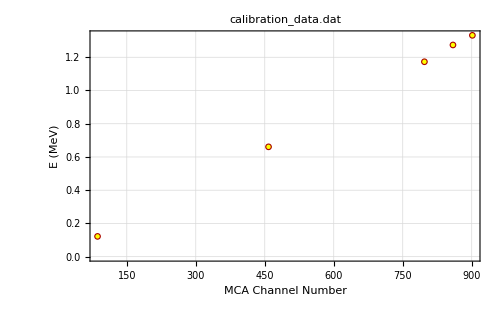

```mathematica
LinearDataPlot[FrameLabel->{"MCA Channel Number","E (MeV)"}]
```

```mathematica
(* We attempt a linear fit. *)
```

```mathematica
LinearFit[]
```

n = 5

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.0119969 | b= 
0.00148981 | 
σ_a= 
0.00740124 | σ_b= 
0.0000106746 | Std. deviation= 
0.00738842

Fit of (x±σ_x,y±σ_y)

a= 
-0.00775362 | b= 
0.00147762 | 
σ_a= 
0.000151915 | σ_b= 
3.58895×10^-7 | χ^2/(n-2)= 
904.393

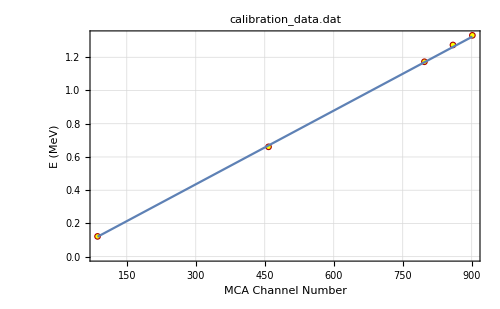
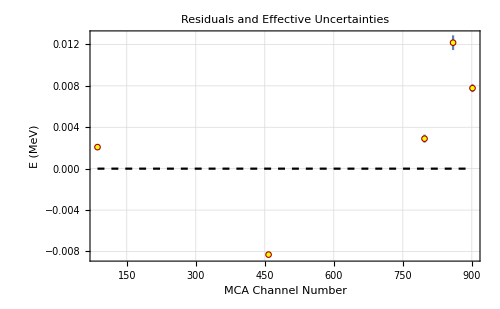
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-0.00775362 | b= 
0.00147762 | 
σ_a= 
0.000151915 | σ_b= 
3.58895×10^-7 | χ^2/(n-2)= 
904.393

```mathematica
LinearDifferencePlot[FrameLabel->{"MCA Channel Number","E (MeV)"}]
```

```mathematica
(* We attempt a quadratic fit. *)
```

```mathematica
QuadraticFit[]
```

n = 5

y(x) = a + b x + c x^2

Fit of (x,y)  (unweighted)

a= 
-0.000253466 | b= 
0.0014058 | c= 
8.4008×10^-8 | 
σ_a= 
0.00556561 | σ_b= 
0.0000288413 | σ_c= 
2.83629×10^-8 | Std. deviation= 
0.00389893

Fit of (x±σ_x,y±σ_y)

a= 
-0.0000261005 | b= 
0.00140492 | c= 
8.28818×10^-8 | 
σ_a= 
0.000207108 | σ_b= 
1.45869×10^-6 | σ_c= 
1.63662×10^-9 | χ^2/(n-3)= 
39.9795

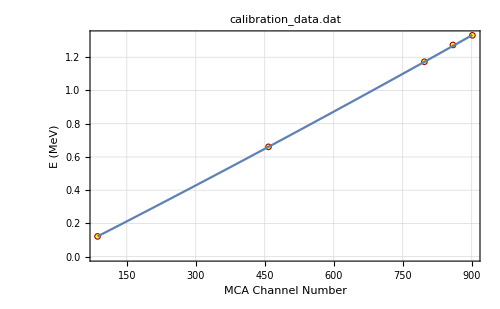
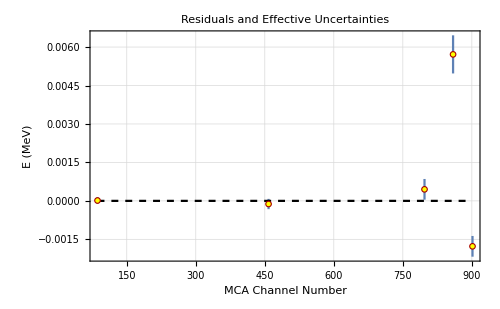
-Graphics-
-Graphics-
y(x) = a + b x + c x^2
a= 
-0.0000261005 | b= 
0.00140492 | c= 
8.28818×10^-8 | 
σ_a= 
0.000207108 | σ_b= 
1.45869×10^-6 | σ_c= 
1.63662×10^-9 | χ^2/(n-3)= 
39.9795

```mathematica
LinearDifferencePlot[FrameLabel->{"MCA Channel Number","E (MeV)"}]
```

```mathematica
(* We attempt a linear fit of only the last 4 data points. *)
```

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{358.107,918.684}

n= 4

1 point removed.

```mathematica
LinearFit[]
```

n = 4

y(x) = a + b x

Fit of (x,y)  (unweighted)

a= 
-0.0350259 | b= 
0.00151861 | 
σ_a= 
0.00825125 | σ_b= 
0.0000106607 | Std. deviation= 
0.00372617

Fit of (x±σ_x,y±σ_y)

a= 
-0.0332233 | b= 
0.00151497 | 
σ_a= 
0.000533104 | σ_b= 
8.35693×10^-7 | χ^2/(n-2)= 
35.8873

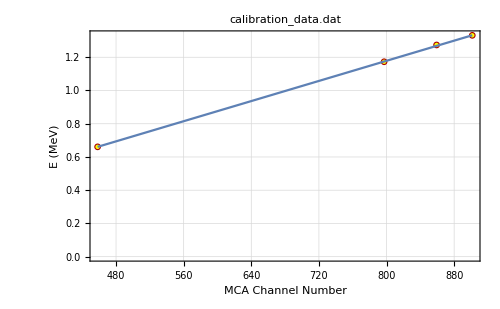
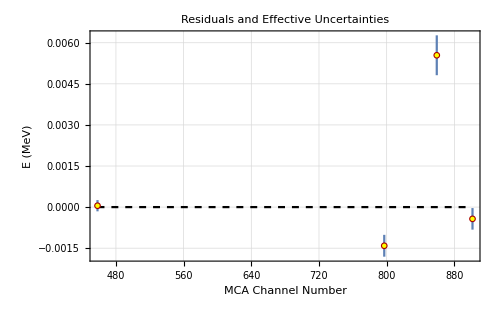
-Graphics-
-Graphics-
y(x) = a + b x
a= 
-0.0332233 | b= 
0.00151497 | 
σ_a= 
0.000533104 | σ_b= 
8.35693×10^-7 | χ^2/(n-2)= 
35.8873

```mathematica
LinearDifferencePlot[FrameLabel->{"MCA Channel Number","E (MeV)"}]
```

We observe high (χ̃)^2 for the fits (of the order of 30-40) because of the unreasonably small error bars we have used. It would be difficult to systematically adjust the error bars for rate-related gain shift, as we do not know the detector’s rate response function, and we do not have information regarding the rate at the detector anyway. Therefore, we simply use the (χ̃)^2 as an order of magnitude measure by which we compare the fits we have obtained above.

We observe that the response for the data points well above 100 keV are well modelled by the linear fit, whereas those closer to and below 100 keV seem better modelled by the quadratic fit. We tentatively define a calibration function as a piecewise of the two functions. We can see that the linear fit and the quadratic fit both have negligible residuals for the data point at channel number 458. Therefore, we chose this to be the point of transition of our piecewise (i.e. our calibration curve will correspond to the quadratic fit for channels 458 and below, and to the linear fit for channels over 458.

```mathematica
(* We define our calibration function. *)
```

```mathematica
calPiecewise[number_]:=Piecewise[{{0.00140492 number+(8.28818*10^-8)number^2,number≤458},{-0.0332233+0.00151497 number,number>458}}]
```

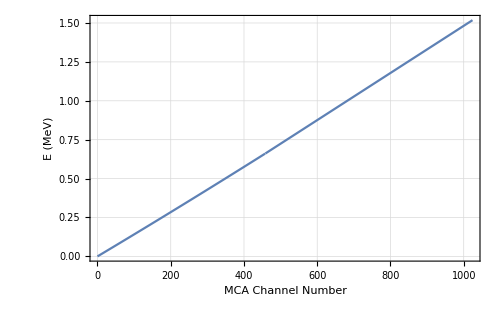

```mathematica
Plot[calPiecewise[x],{x,0,1024},FrameLabel->{"MCA Channel Number","E (MeV)"}]
```

Note that even though this is the best we can come up with from the calibration data we have, this function is not very reliable at low energies, since we only have one data point for the seemingly quadratic region.

We observe above from the order of magnitude of the σ’s that uncertainties in peak positions originating from the statistical nature of the data contribute negligibly to uncertainties in our calibration. As we will see below, we will in fact neglect those in favor of much more significant sources of uncertainty.

## Identifying and finding the energies of features using the calibration

### Na-22 positron annihilation peak

```mathematica
(* We first identify as before the channel location of the annihilation peak. *)
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/na22.tsv

File comment header:

Spectrum Name:
Description:
Student ID:
Detector Used:
Comments:
Acquisition Mode:	PHA
High Voltage:	920
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.15
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	650.45
Live Time Elapsed:	648.97
Start Time:	04/12/2018 14:36:48
Stop Time:	04/12/2018 14:47:47

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
MakePoisson[Xerrors -> True]
```

Sorted data in order of increasing X values.

1024 Y count values have had sigma values assigned.

1024 X channel values have had sigma values assigned.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{341.,371.2}

n= 31

993 points removed.

```mathematica
GaussianLFit[]
```

n = 31

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y)  (unweighted)

Calculating sigs

c= 
-6.51933 | d= 
-9.59241 |  | 
σ_c= 
247.713 | σ_d= 
4.56019 |  | 
y_max= 
1595.3 | μ= 
356.809 | sigma= 
12.1711 | 
σ_y_max= 
416.728 | σ_μ= 
0.62686 | σ_sigma= 
2.05593 | Std. deviation= 
40.0051

Fit of (x,y±σ_y)

c= 
-10.3173 | d= 
-8.91585 |  | 
σ_c= 
358.17 | σ_d= 
3.6381 |  | 
y_max= 
1598.57 | μ= 
356.702 | sigma= 
12.1995 | 
σ_y_max= 
363.636 | σ_μ= 
0.525117 | σ_sigma= 
1.59997 | χ^2/(n-5)= 
1.29338

Fit of (x±σ_x,y±σ_y)

c= 
-10.3182 | d= 
-8.9165 |  | 
σ_c= 
358.209 | σ_d= 
3.64034 |  | 
y_max= 
1598.58 | μ= 
356.703 | sigma= 
12.1994 | 
σ_y_max= 
363.84 | σ_μ= 
0.52538 | σ_sigma= 
1.59897 | χ^2/(n-5)= 
1.29293

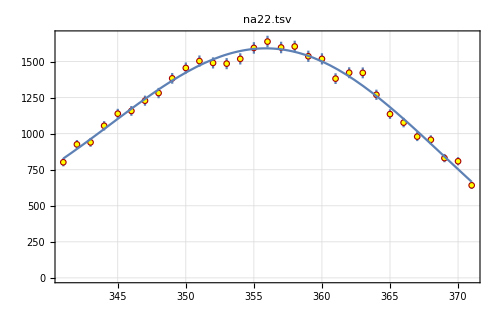
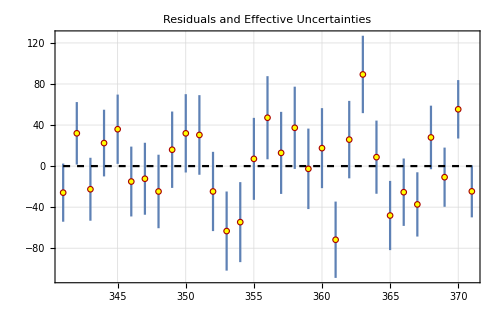
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
-10.3182 | d= 
-8.9165 |  | 
σ_c= 
358.209 | σ_d= 
3.64034 |  | 
y_max= 
1598.58 | μ= 
356.703 | sigma= 
12.1994 | 
σ_y_max= 
363.84 | σ_μ= 
0.52538 | σ_sigma= 
1.59897 | χ^2/(n-5)= 
1.29293

```mathematica
LinearDifferencePlot[]
```

```mathematica
(* We observe that the annihilation peak occurs at channel μ = 356.7, and we can use the calibration function to find the corresponding energy. *)
```

```mathematica
annihilationEnergy=NumberForm[calPiecewise[356.703],4] (* MeV *)
```

0.5117

We have no information regarding the count-rate and difference in rates for the two data points we took to investigate rate-dependent gain-shift, or regarding the count rates for our other spectra. We only have a single data point regarding the gain shift, making it difficult to quantify the error induced by this shift in our calibration model. The simplest choice here is to assume that the gain function is linear (we have seen that this is not quite the case, but should be a good enough approximation to give us an idea of the error induced) and assume that the shift measured is representative of the error in peak position for that peak due to rate-related gain shift (we have no way of finding out if this is correct, but it is the only data point we have and therefore the only guess we can make). Then we use the shift to estimate the fractional uncertainty in the peak position, which by our assumptions should then be the uncertainty in the gain and therefore the fractional uncertainty in the position of our other features as well (including the annihilation peak for Na-22 we are interested in).

```mathematica
fractionalUncertainty=(13/458)//N
```

0.0283843

```mathematica
uncertaintyAnnihilation=fractionalUncertainty*356.7
```

10.1247

```mathematica
calPiecewise[366.8]-calPiecewise[356.7]
```

0.0147953

```mathematica
calPiecewise[346.6]-calPiecewise[356.7]
```

-0.0147784

By the above, we then have the energy of the positron annihilation peak as 0.512 ± 0.015 MeV. However, there are also errors induced by time-drift of the gain, as measured above. This time again, we only have a single data point to investigate the shift, and therefore do not know the time-scale of the variation of the gain. However, the very good Gaussian+Linear fits we have obtained over relatively long run-times suggest that the time scale is relatively long (otherwise the spectra would have been distorted and we would not have obtained clean fits), so we treat the error induced by the time-drift of gain as a systematic error, separate from the error above. We again resort to the same assumptions as above to estimate the systematic error.

```mathematica
fractionalSystematic=(4/798)//N
```

0.00501253

```mathematica
systematicAnnihilation=fractionalSystematic*797.5
```

3.99749

```mathematica
calPiecewise[360.7]-calPiecewise[356.7]
```

0.00585752

```mathematica
calPiecewise[352.8]-calPiecewise[356.7]
```

-0.00570853

We then have the energy of the positron annihilation peak as 0.512 ± 0.015 ± 0.006 MeV, which should also correspond to the rest energy of the electron. While our estimates for the error bars are admittedly rough, hardly rigorous and may be unreliable, here we find that we are within error of the accepted value for m_e = 0.510999 MeV.

### Compton edge for Cs-137

We expect the Compton edge to occur at T_e=0.4773 MeV. We use our calibration function to find the channel that this energy corresponds to:

```mathematica
NSolve[calPiecewise[channel]==0.4773&&channel>0,channel]
```

{{channel→333.186}}

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"spectrum files"->{"*.tsv"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, SkipLines->{"Data:","Counts"}]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/3_Spring_2018/Ph7/Experiment 30a/cesium137.tsv

File comment header:

Spectrum Name:
Description:
Student ID:
Detector Used:
Comments:
Acquisition Mode:	PHA
High Voltage:	920
Conversion Gain:	1024
Course Gain:	8
Fine Gain:	1.15
ULD:	106.2%
LLD:	0.0%
Calibration Coefficients:
Channels used to calibrate:
Energies used to calibrate:
Real Time Elapsed:	729.15
Live Time Elapsed:	707.71
Start Time:	04/12/2018 14:05:16
Stop Time:	04/12/2018 14:17:25

ROIs:
Number	Low	High	Gross	Net	FWHM	Centroid

Data:

Read 1024 data points.

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{202.,403.2}

n= 202

822 points removed.

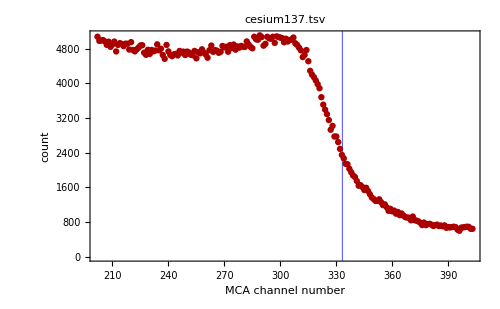
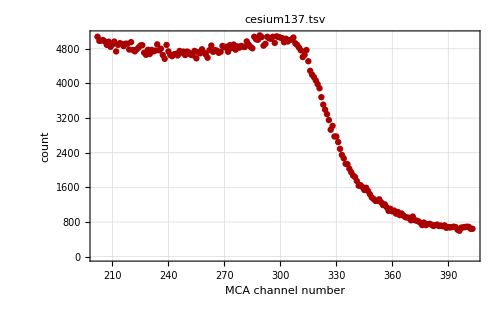

```mathematica
Overlay[{LinearDataPlot[FrameLabel->{"MCA channel number","count"},GridLines->{{333.186},{}},GridLinesStyle->Blue],LinearDataPlot[FrameLabel->{"MCA channel number","count"}]}]
```

The vertical blue line represents the channel corresponding to T_e, the expected energy at which the Compton edge occurs. We observe that a little more than halfway down from the peak of the hump (as opposed to the expected location about 1/3 of the way down shown in the lab manual). This may be due to the error in the calibration function.

### Backscatter feature

```mathematica
Undo[]
```

cesium137.tsv

n = 1024

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> False, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{59.4,219.8}

n= 160

864 points removed.

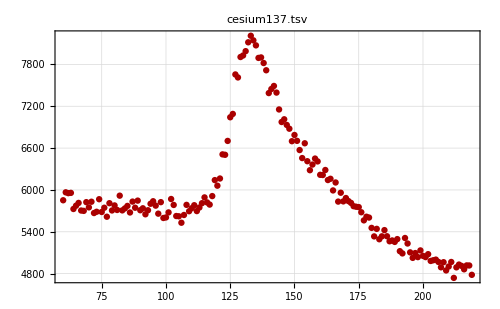

```mathematica
LinearDataPlot[]
```

```mathematica
(* We observe that the backscatter feature is located at the maximum point of our dataset. By opening the data table, we find that this is the point corresponding to the MCA channel 133. *)
```

```mathematica
backscatterEnergy=calPiecewise[133] (* MeV *)
```

0.18832

We recall that in the pre-lab we calculated a backscattering energy of 0.1843 MeV. Our estimate of 0.1883 MeV based on the location of the peak is therefore within ~2.2% of the expected energy of the backscattering peak, which again is consistent with the error in our calibration function. Indeed, we can find the error bars on our estimate as before:

```mathematica
uncertaintyBackscatter=fractionalUncertainty*133
```

3.77511

```mathematica
calPiecewise[133+3.775]-calPiecewise[133]
```

0.00538798

```mathematica
calPiecewise[133-3.775]-calPiecewise[133]
```

-0.00538562

```mathematica
systematicBackscatter=fractionalSystematic*133
```

0.666667

```mathematica
calPiecewise[133+0.6666]-calPiecewise[133]
```

0.000951253

```mathematica
calPiecewise[133-0.6666]-calPiecewise[133]
```

-0.000951179

and from this we obtain an estimate with uncertainty for the backscattering energy of 0.188 ± 0.005 ± 0.001 MeV, and indeed we are within error of the expected value.